# Synchronisation (version 20-10-2021)

## FSSP - Firing Squad Synchronisation Problem

A CA that, starting with a single active cell, eventually reaches a state in which all cells are simultaneously active. It is an analogy of the situation where an officer commands an execution, so that the soldiers fire their rifles simultaneously.

### Plot

```mathematica
FiringSquad[n_]:=CellularAutomaton[{73897141112273431645813993997840119510301349955844120053108303402869288252883208765282258700427663553231606219461134537609654452239997158715057071744303981189720289616900828369511226411463607725250428864754483628990603215225935923342255545722542581344662672444056783344087384592424383474777,7},Flatten[{6,3,Table[0,{n-1}],6}],2 n-2]
```

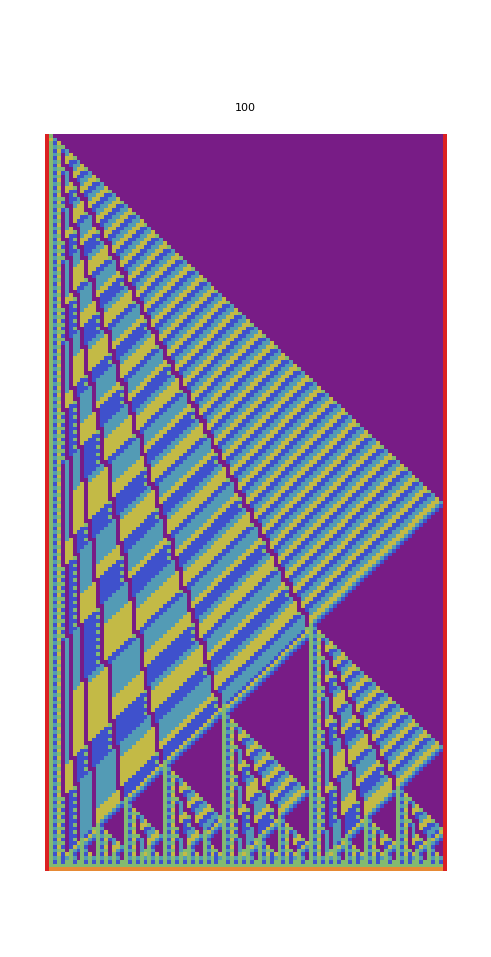

```mathematica
ArrayPlot[FiringSquad[100], PlotLabel->ToString[100],ColorFunction->ColorData["Rainbow"]]
```

### More detail:

https://en.wikipedia.org/wiki/Firing_squad_synchronization_problem

## A very good r=3 rule in the binary synchronisation problem

Hexadecimal rule number, with state transitions defined in the opposite Wolfram’s lexicographical order: FEB1C6EAB8E0C4DA6484A5AAF410C8A0
G.M. Oliveira, L.G. Martins, L.B. de Carvalho, E. Fynn. “Some investigations about synchronization and density classification tasks in one-dimensional and two-dimensional cellular automata rule spaces”. Electronic Notes in Theoretical Computer Science 252:121–142, 2009.
https://doi.org/10.1016/j.entcs.2009.09.018

```mathematica
ArrayPlot@CellularAutomaton[{6744959628743063613936427865158684031,2,3},RandomInteger[{0,1},149],200]
```

-Graphics-

```mathematica
Module[{ic=RandomInteger[1,7],neighbourhoods={},icprevious},
icprevious=ic;
NestWhileList[
(icprevious=ic;
neighbourhoods=Join[neighbourhoods,{Take[#,-7]}];
ic=Append[#,Cases[RuleTable[6744959628743063613936427865158684031,2,3],{Take[#,-7],_}]⟦1,-1⟧])&,
ic,
(Print@neighbourhoods;
Print@Take[icprevious,-7];
¬MemberQ[neighbourhoods,Take[icprevious,-7]])]]
```

{}

{1,0,0,1,0,1,1}

{{1,0,0,1,0,1,1}}

## A family of initial configurations that make any 1D rule, with arbitrary r-radius and k-states fail in the synchronisation problem

Construction according to:
N. Fatès. “Remarks on the cellular automaton global synchronisation problem: deterministic versus stochastic models”. Natural Computing, May 2018.
https://doi.org/10.1007/s11047-018-9683-0

```mathematica
SynchProblemFailure[rnum_Integer,k_Integer: 2,r_: 1]:=
Module[{ic=RandomInteger[k-1,⌊2r+1⌋],neighbourhoods={},neighsize=⌊2r+1⌋,icprevious,loopedNeighbourhoods,loopedIC},
icprevious=ic;
While[¬MemberQ[neighbourhoods,Take[icprevious,-neighsize]],
neighbourhoods=Join[neighbourhoods,{Take[ic,-neighsize]}];
ic=Append[ic,Cases[RuleTable[rnum,k,r],{Take[ic,-neighsize],_}]⟦1,-1⟧];
icprevious=ic];
loopedNeighbourhoods=Take[neighbourhoods,{Position[neighbourhoods,Take[ic,-neighsize]]⟦1,1⟧,-1}];
Print@loopedNeighbourhoods;
loopedIC=Cases[RuleTable[rnum,k,r],{#,_}]⟦1,-1⟧&/@loopedNeighbourhoods;
Print@loopedIC;
{ArrayPlot[loopedNeighbourhoods],ArrayPlot@CellularAutomaton[{rnum,k,r},loopedIC,5Length[loopedIC]]}];
```

{{0,1,1,0,0,0,1},{1,1,0,0,0,1,1},{1,0,0,0,1,1,1},{0,0,0,1,1,1,0},{0,0,1,1,1,0,0},{0,1,1,1,0,0,1},{1,1,1,0,0,1,1},{1,1,0,0,1,1,0},{1,0,0,1,1,0,0},{0,0,1,1,0,0,0}}

{1,1,0,0,1,1,0,0,0,1}

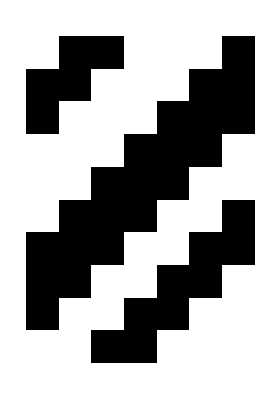
{-Graphics-,-Graphics-}

```mathematica
SynchProblemFailure[6744959628743063613936427865158684031,2,3]
```

{{2,0,0},{0,0,0},{0,0,2},{0,2,0}}

{0,2,0,0}

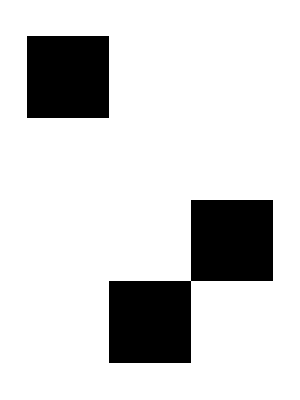
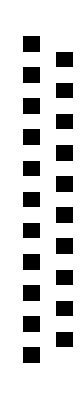

```mathematica
SynchProblemFailure[6744959,3,1]
```

{{0,0,0,0,0,0,0},{0,0,0,0,0,0,2},{0,0,0,0,0,2,2},{0,0,0,0,2,2,1},{0,0,0,2,2,1,0},{0,0,2,2,1,0,2},{0,2,2,1,0,2,0},{2,2,1,0,2,0,0},{2,1,0,2,0,0,0},{1,0,2,0,0,0,0},{0,2,0,0,0,0,0},{2,0,0,0,0,0,0}}

{2,2,1,0,2,0,0,0,0,0,0,0}

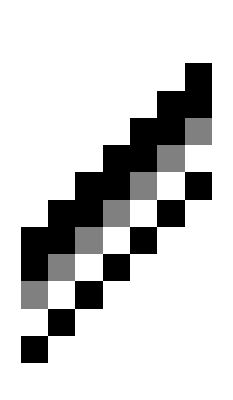
{-Graphics-,-Graphics-}

```mathematica
SynchProblemFailure[6744959628743063613936427865158684031,3,3]
```

## Asynchronous solution for the binary synchronisation problem, with radius-1.5 rule 4959 and update schedule {{1}, {2, 3, 4, ..., N}}.

E.L.P. Ruivo, P.P. Balbi and K. Perrot.  “An asynchronous solution to the synchronisation problem for binary one-dimensional cellular automata”, Physica-D, vol. 413, article 132554, 2020.

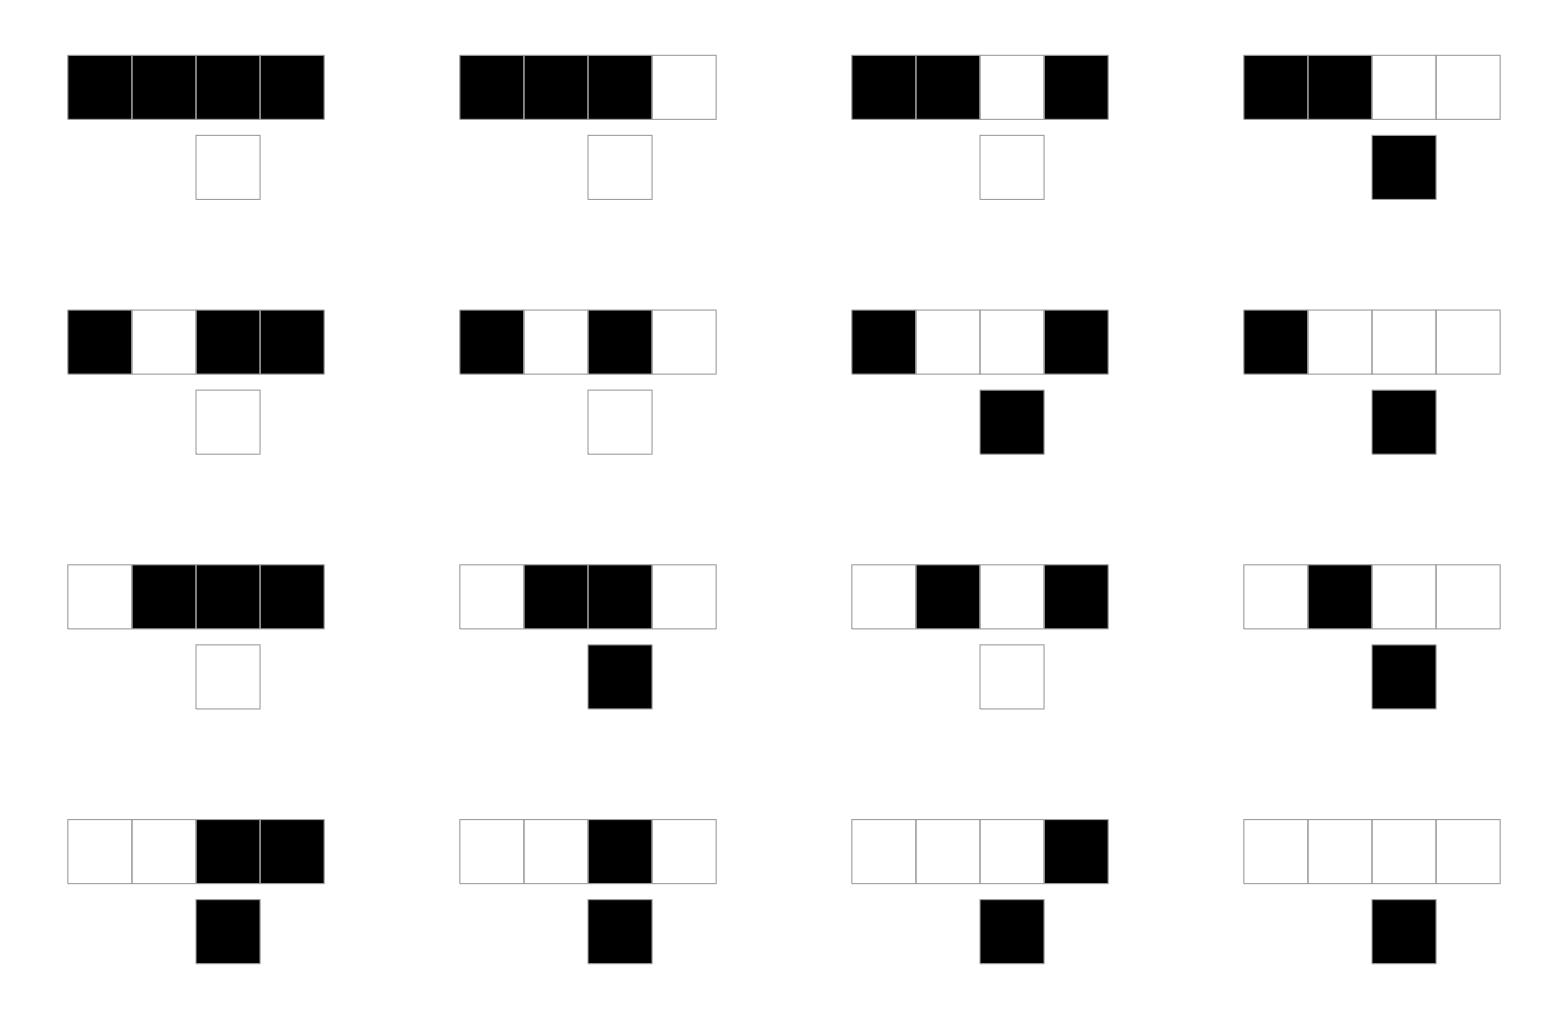

```mathematica
RulePlot[CellularAutomaton[{4959,2,3/2}]]
```

```mathematica
Module[{icaux=RandomInteger[{0,1},50],tsteps},
tsteps=⌈2.2 Length[icaux]⌉;
ArrayPlot[AsynchronousCA[{4959,2,3/2},icaux,tsteps,{{1},Range[2,Length[icaux]]}],Mesh->False]]
```

-Graphics-

## Synchronous solution for the binary synchronisation problem, with a non-homogeneous CA made up with elementary rules 51 and 15: (51, 15, 15, ..., 15).

Suggested by one the reviewers of our paper above in Physica D. 
But, originally present in: M. Sipper. “Computing with cellular automata: Three cases for nonuniformity”, Physical Review E 57(3):3589-3592, 1998.

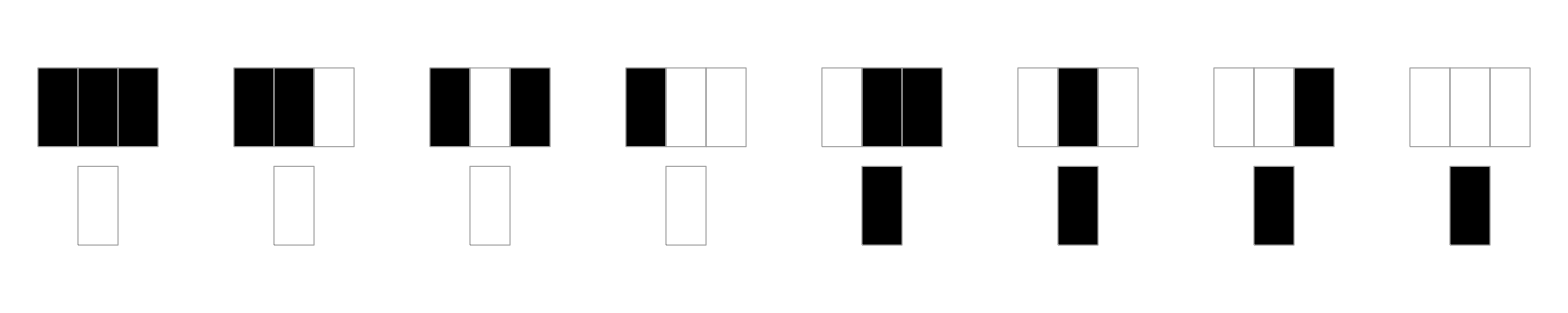

```mathematica
RulePlot[CellularAutomaton[15]]
```

```mathematica
Module[{icLen=50,icaux,tsteps},
icaux=RandomInteger[{0,1},icLen];
tsteps=⌈2 icLen⌉;
ArrayPlot[CASpatialComposition[Join[{{51,2,1}},Table[{15,2,1},icLen-1]],icaux,tsteps],Mesh->False]]
```

-Graphics-

### Considering a single initial configuration, the dynamics of the two solutions is not necessarily the same:

```mathematica
Module[{icLen=50,icaux,tsteps},
icaux=RandomInteger[{0,1},icLen];
tsteps=⌈2 icLen⌉;
{ArrayPlot[CASpatialComposition[Join[{{51,2,1}},Table[{15,2,1},icLen-1]],icaux,tsteps],Mesh->False],ArrayPlot[AsynchronousCA[{4959,2,3/2},icaux,tsteps,{{1},Range[2,icLen]}],Mesh->False]}]
```

{-Graphics-,-Graphics-}

### Considering the set of all initial configurations of a given size, the dynamics of the two solutions is different:

```mathematica
Sort[Module[{icLen=4,icaux=#,tsteps},
tsteps=⌈2 icLen⌉;
CASpatialComposition[Join[{{51,2,1}},Table[{15,2,1},icLen-1]],icaux,tsteps]]&/@Tuples[{0,1},4]]==
Sort[Module[{icLen=4,icaux=#,tsteps},
tsteps=⌈2 icLen⌉;
AsynchronousCA[{4959,2,3/2},icaux,tsteps,{{1},Range[2,icLen]}]]&/@Tuples[{0,1},4]]
```

False

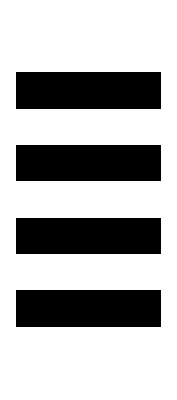
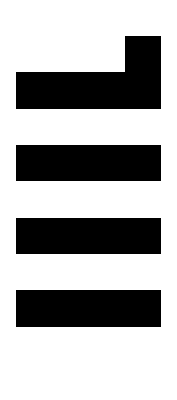
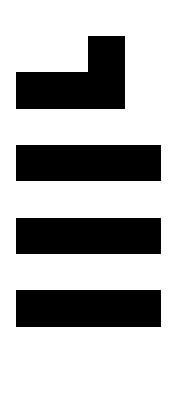
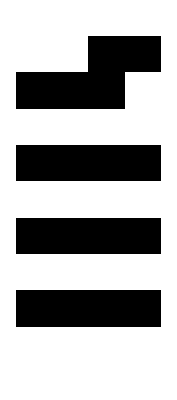
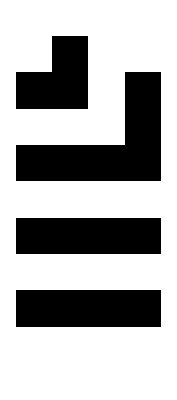
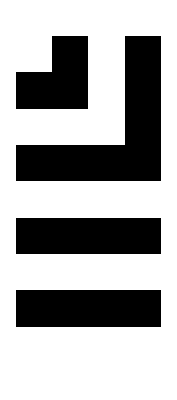
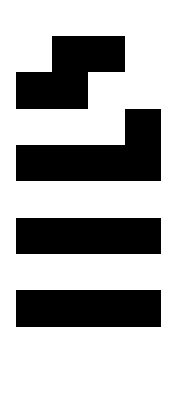
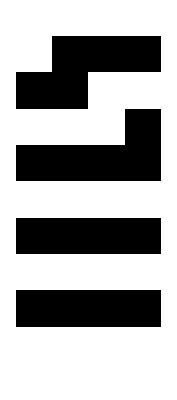

```mathematica
ArrayPlot/@Sort[Module[{icLen=4,icaux=#,tsteps},
tsteps=⌈2 icLen⌉;
CASpatialComposition[Join[{{51,2,1}},Table[{15,2,1},icLen-1]],icaux,tsteps]]&/@Tuples[{0,1},4]]
```

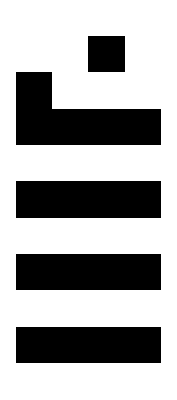
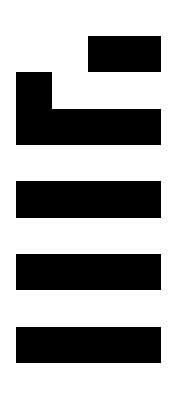
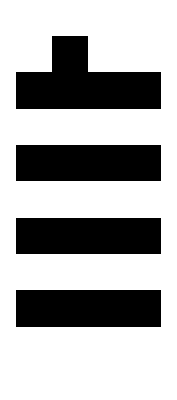
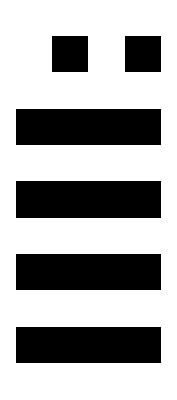
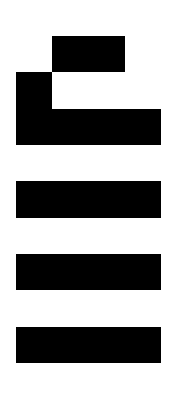
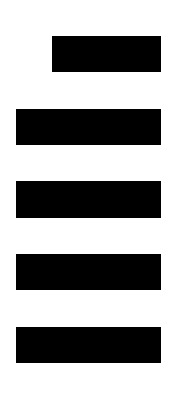
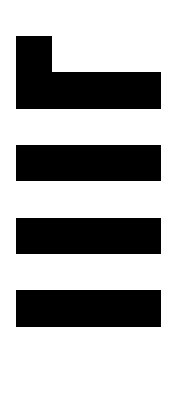
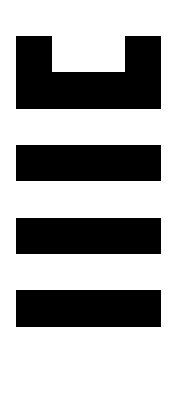
{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
ArrayPlot/@Sort[Module[{icLen=4,icaux=#,tsteps},
tsteps=⌈2 icLen⌉;
AsynchronousCA[{4959,2,3/2},icaux,tsteps,{{1},Range[2,icLen]}]]&/@Tuples[{0,1},4]]
```